# Genetic Algorithm for PIA

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["CAGD`","CAGD.wl"];
```

## Matrix Multiplication

```mathematica
GetMatrix[set_] := Module[{},
	If[set[[1]] == 0,Return[TranslationM[set[[2]],set[[3]]]]];
	If[set[[1]] == 1,Return[ScalingM[set[[2]],set[[3]]]]];
	(*If[set[[1]] == 3,Return[RotationM[set[[4]] Degree]]];*)
	If[set[[1]] == 2,Return[ShearXM[set[[4]] Degree]]];
	If[set[[1]] == 3,Return[ShearYM[set[[4]] Degree]]];
];
```

```mathematica
MatMul[points_, mats_] := Module[{newPoints, k,i, midPoint, mat},
	newPoints =  Append[#, 1] & /@ points;
	midPoint = (newPoints[[1]] + newPoints[[Length[newPoints]]])/2;
	newPoints = Table[newPoints[[i]] - midPoint + {0,0,1}, {i,1,Length[points]}];
	For[i = 1, i <= Length[mats],i++,
		mat = Decoding[mats[[i]]];
		newPoints = Table[GetMatrix[mat]. newPoints[[k]], {k,1,Length[points]}];
	];
	newPoints = Table[newPoints[[k]] + midPoint - {0,0,1}, {k,1,Length[points]}];
	Return[newPoints];
];
```

```mathematica
points = {{1,2}, {3,4}, {5,5}};
```

```mathematica
GeneratePopulation[22, 5, 3][[1,;;-2]]
```

{{0,1,0,0,0,1,1,0,0,1,1,0,0,1,1,1,0,1,1,0,1,1},{1,0,0,0,1,1,0,0,0,0,0,1,0,0,1,1,0,1,0,1,0,1},{1,0,0,0,0,1,1,1,1,0,1,0,1,0,1,1,0,0,0,1,0,1},{0,0,0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,1},{1,0,1,0,0,1,1,1,0,1,1,1,0,1,1,0,0,1,0,0,0,1}}

```mathematica
N[MatMul[points, GeneratePopulation[22, 5, 3][[1,;;-2]]]]
```

{{127.419,5.02113,1.},{50.1937,71.7667,1.},{-19.419,97.4103,1.}}

## Generate Random Set

```mathematica
GeneratePopulation[nBit_, nMat_, nPop_] := Module[{matL, i, temp},
	matL = {};
	For[i = 1, i <= nPop, i++,
		temp = RandomInteger[1, {nMat, nBit}];
		AppendTo[temp, 0];
		AppendTo[matL, temp];
	];
	Return[matL];
]
```

```mathematica
GeneratePopulation[22, 5, 3][[1]]
```

{{0,1,0,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1},{0,1,0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,1,1,1,0,0},{0,1,0,0,0,0,0,0,0,0,1,0,1,1,1,1,0,0,1,1,1,1},{1,1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,1,0,1,0,0,1},{0,1,1,0,1,0,1,1,0,0,1,1,0,1,1,1,0,1,1,1,0,0},0}

## Decoding

```mathematica
Decoding[mat_] := Module[{typeIdxList, xIdxList, yIdxList, angIdxList, type, x, y, ang},
	(*get indics of each parameter*)
	typeIdxList = {1, Length[mat]};
	xIdxList = Select[Range[Length[mat]],(# != 1 && # != Length[mat] && Mod[#,3] == 2)&];
	yIdxList = Select[Range[Length[mat]],(# != 1 && # != Length[mat] && Mod[#,3] == 0)&];
	angIdxList = Select[Range[Length[mat]],(# != 1 && # != Length[mat] && Mod[#,3] == 1)&];
	
	(*decode*)
	type = FromDigits[Table[mat[[typeIdxList[[i]]]],{i, 1, Length[typeIdxList]}], 2];
	x = FromDigits[Table[mat[[xIdxList[[i]]]], {i, 2, Length[xIdxList]}], 2];
	y = FromDigits[Table[mat[[yIdxList[[i]]]], {i, 2, Length[yIdxList]}], 2];
	ang = FromDigits[Table[mat[[angIdxList[[i]]]], {i, 2, Length[angIdxList]}], 2];
	
	(*check sign*)
	x = If[mat[[xIdxList[[1]]]] == 1, -x, x];
	y = If[mat[[yIdxList[[1]]]] == 1, -y, y];
	ang = If[mat[[angIdxList[[1]]]] == 1, -ang, ang];
	
	Return[{type, x, y, ang}];
]
```

```mathematica
Decoding[{0,1,1,1,1,1,0,1,1,1,1,0,0,1,0,0,0,0,1,1,0,1}]
```

{1,-61,-48,-9}

## Fitness Function & Termination Criteria

```mathematica
TerminationCriteria[controlPoints_, testPoints_, ϵ_ ] := Module[{n, t, poc, Δ, tol, status, x,i},
	n = Length[controlPoints];
	t = Table[i/(n-1), {i, 0, n-1}];
	poc = Table[Bezier[SetC1n[controlPoints, testPoints], x] /. x->t[[i]], {i,1,n}];
	Δ = controlPoints - poc;
	tol = Max[Table[Norm[Δ[[i]]], {i, 1, n}]];  (*fitness score*)
	(*tol = Norm[Table [Norm[Δ[[i]]], {i, 1, n}]];*)
	If[tol < ϵ, status = True, status = False];
	Return[{status, tol}];
];
```

```mathematica
GetFitnessScore[controlPoints_, testSet_, nMatrix_,  ϵ_] := Module[{newPoints, newTestSet,i, transformedPoints},
	newTestSet = testSet;
	For[i = 1, i <= Length[testSet], i++,
		transformedPoints = N[MatMul[controlPoints, testSet[[i, ;;-2]]]][[All, ;;2]];
		newTestSet[[i, nMatrix+1]] = TerminationCriteria[controlPoints, transformedPoints, ϵ][[2]];
	];
	Return[newTestSet];
];
```

```mathematica
GetFitnessScore[{{17,71},{1,39},{32,50},{97,55}}, GeneratePopulation[22, 5, 3], 5, 1]
```

{{{1,0,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,0,1,1,0,0},{0,1,0,1,0,0,0,1,1,0,0,0,0,1,0,0,1,1,1,0,0,0},{1,0,1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,1,1,1,1,1},{0,1,0,0,0,1,0,1,0,0,1,1,1,0,0,0,1,0,1,0,1,1},{1,1,0,1,0,1,1,0,1,1,1,0,0,1,1,1,0,1,0,0,1,0},1457.33},{{1,1,0,0,1,0,1,1,1,1,0,0,0,1,0,0,1,1,1,1,0,1},{1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,1,0,0,1},{0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,1,1,1,1,1,1,1},{1,0,1,1,0,0,1,0,0,1,0,1,1,1,1,1,1,1,1,0,1,1},{1,0,0,0,0,1,0,1,1,0,0,1,0,0,1,1,0,0,1,1,1,1},1569.73},{{0,1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,0,1,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0},{1,1,0,1,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,1,0},{1,1,1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,0},{1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,1,0,1,1,0,1,1},18.5851}}

```mathematica
(*GetFitnessScore[controlPoints_, guessSet_, testSet_, nMatrix_,  ϵ_] := Module[{newPoints, newTestSet, i, j, transformedPoints, fitnessScore, guessSetTransformedPoints},
	newTestSet = testSet;
	For[i = 1, i <= Length[newTestSet], i++,
		fitnessScore = 0;
		For[j = 1, j <= Length[guessSet], j++, 
			transformedPoints = N[MatMul[controlPoints, testSet[[i, ;;nMatrix]]]][[All, ;;2]];
			guessSetTransformedPoints = N[MatMul[controlPoints, guessSet[[j, ;;nMatrix]]]][[All, ;;2]];
			(*Print[testSet[[i, ;;nMatrix]]];*)
			fitnessScore = fitnessScore + Abs[TerminationCriteria[guessSetTransformedPoints, transformedPoints, ϵ][[2]] - guessSet[[j, -1]]];
		];
		newTestSet[[i, nMatrix+1]] = fitnessScore;
	];
	Return[newTestSet];
];*)
```

```mathematica
tSet = {{{3.,26.,25.,13.,-32.},{35.,8.,38.,56.,-21.},{3.,16.,16.,-12.,30.},{29.,24.,25.,84.,-32.},{5.,7.,34.,-66.,71.},0}};
gSet = {{{2,41,10,-89,11},{4,17,1,-50,3},{4,21,40,46,66},{3,15,21,14,10},{1,49,17,14,-58},616.0332254187018}};
```

## Evolution Method

### Parent Selection

#### Roulette Wheel Selection

```mathematica
RouletteWheelSelection[mSet_, nParent_] := Module[{n, newmSet, cumFitnessScore, selPoint, i, j, cumSum, parent = {}, invertedFitness},
  n = Length[mSet];
  newmSet = mSet;
  invertedFitness = 1 / newmSet[[All, -1]];
  
  For[i = 1, i <= nParent, i++,
    cumFitnessScore = N[Total[invertedFitness]];
    selPoint = RandomReal[{0, cumFitnessScore}];
    cumSum = 0;
    
    For[j = 1, j <= n, j++,
      cumSum += invertedFitness[[j]];
      If[cumSum >= selPoint,
        AppendTo[parent, newmSet[[j]]];
        invertedFitness = Delete[invertedFitness, j]; 
        newmSet = Delete[newmSet, j];
        Break[];
      ];
    ];
    n--;
  ];
  
  Return[parent];
];
```

```mathematica
ppopSet = GeneratePopulation[22, 5, 10];
ppopSet = GetParentFitnessScore[{{17,71},{1,39},{32,50},{97,55}}, ppopSet, 5, 1];
```

```mathematica
RouletteWheelSelection[ppopSet, 2]
```

{{{0,0,0,1,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0},{1,1,0,1,0,1,0,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1},{0,0,1,1,1,1,0,0,0,0,1,0,1,0,1,1,0,1,0,1,1,0},{0,1,0,1,0,0,1,0,0,1,1,0,1,0,0,1,0,1,0,0,0,0},{1,0,1,1,0,1,0,0,1,0,0,1,1,0,0,1,0,1,1,1,1,1},48.1827},{{0,0,1,0,0,1,1,1,0,1,1,1,1,0,1,1,0,1,1,1,1,0},{1,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,0,0,1,0,1},{1,0,0,1,0,1,1,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1},{1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0,1,0,1},{1,1,1,1,0,0,0,0,1,1,1,0,1,1,1,1,1,0,0,1,0,0},47.757}}

#### Stochastic Universal Sampling

```mathematica
StochasticUniversalSampling[mSet_,nParent_]:=Module[{n, newmSet, cumFitnessScore, selPoint, i, j, cumSum, parent={}, stepSize, startPoint, points, invertedFitness, totalFitness},
	n = Length[mSet];
	newmSet = mSet;
	invertedFitness = 1 / newmSet[[All, -1]];
	cumFitnessScore = Accumulate[invertedFitness];
	totalFitness = Last[cumFitnessScore];
	stepSize = totalFitness / nParent;
	startPoint = RandomReal[{0, stepSize}];
	points = Table[startPoint + (i - 1) stepSize, {i, nParent}];
	j = 1;
	For[i = 1, i <= nParent, i++,
	    While[points[[i]] > cumFitnessScore[[j]],
	      j++;
	    ];
	    AppendTo[parent, newmSet[[j]]];
	];
	Return[parent];
];
```

```mathematica
StochasticUniversalSampling[ppopSet , 2];
```

#### Tournament Selection

```mathematica
TournamentSelection[mSet_, nParent_] := Module[{n ,k, min, parent={}, i, j, candIdxList, newmSet, winner},
	n = Length[mSet];
	k = 0.1;
	min = 5;
	For[i = 1, i <= nParent, i++,
		newmSet = mSet;
		While[Length[newmSet] > min,
			candIdxList = RandomInteger[{1, Length[newmSet]}, Floor[k*Length[newmSet]]];
			newmSet = newmSet[[candIdxList]];
		];
		AppendTo[parent, Sort[newmSet][[-1]]];
	];
	Return[parent];
];
```

```mathematica
TournamentSelection[ppopSet,2]
```

{{{0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,1},{0,1,1,1,1,1,1,0,0,0,1,1,1,1,0,0,0,1,1,1,1,0},{0,1,1,1,1,1,0,0,0,1,1,0,0,0,0,1,1,1,1,1,0,0},{1,1,0,0,0,1,1,1,1,0,1,1,0,1,1,1,0,1,1,0,0,1},{0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,1,1,1,1,1,0,1},16936.7},{{1,1,0,0,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,1,0,1},{0,1,1,1,0,1,1,0,1,1,0,0,1,0,0,0,0,0,1,1,0,0},{0,0,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1,0,1,0,1,1},{1,0,0,1,1,1,0,0,1,0,1,1,1,1,1,1,0,1,1,1,1,0},{1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,1,1,1},1892.99}}

#### Rank Selection

### Crossover Method

#### Uniform crossover

```mathematica
UniformCrossover[p_ ,q_ ] := Module[{i, temp, c1, c2, m, n, prob},
	m = Length[p];
	n = Length[p[[1]]];
	c1 = Flatten[p];
	c2 = Flatten[q];
	For[i = 1, i <= m*n, i++,
		prob = RandomInteger[{1,100}]/100;
		If[prob > 0.5,
			temp = c1[[i]];
			c1[[i]] = c2[[i]];
			c2[[i]] = temp;
		];
	];
	Return[{ArrayReshape[c1, {m,n}],ArrayReshape[c2, {m,n}]}];
]
```

```mathematica
offsprings = GeneratePopulation[22, 5, 10][[;;2]]
UniformCrossover[offsprings[[1, ;;-2]], offsprings[[2, ;;-2]]]
```

{{{0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,1,0,1,1,0,0},{1,1,0,0,1,1,1,1,0,1,0,1,1,0,0,1,0,0,1,1,1,1},{0,1,1,1,0,1,1,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0},{0,0,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,0,0,1},{1,1,1,0,0,1,0,1,0,1,0,0,1,1,1,0,0,1,1,0,1,0},0},{{0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0},{1,0,1,0,1,0,1,1,1,1,1,0,0,1,0,0,1,0,1,0,0,1},{1,0,1,1,0,1,1,1,1,0,1,0,0,1,1,1,1,1,0,0,1,0},{0,0,0,1,0,0,1,0,1,1,0,1,0,0,1,0,0,0,1,1,1,0},{0,1,0,1,1,1,0,0,0,1,0,0,1,1,0,0,0,1,1,1,0,1},0}}

{{{0,0,1,0,0,0,1,1,1,1,0,0,1,1,0,1,0,0,1,1,1,0},{1,1,0,0,1,1,1,1,1,1,0,0,1,1,0,1,0,0,1,1,1,1},{1,0,1,1,0,1,1,0,1,0,0,0,0,1,1,0,0,1,0,0,1,0},{0,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,1,1,0,1,1},{1,1,1,0,1,1,0,0,0,1,0,0,1,1,1,0,0,1,1,1,1,0}},{{0,0,1,1,1,0,1,1,0,0,0,1,0,0,0,0,1,1,1,0,0,0},{1,0,1,0,1,0,1,1,0,1,1,1,0,0,0,0,1,0,1,0,0,1},{0,1,1,1,0,1,1,1,1,0,1,0,1,1,1,1,1,0,0,0,1,0},{0,0,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,0},{0,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1,0,0,1}}}

#### N-point crossover

```mathematica
Range[1,100, 5]
```

{1,6,11,16,21,26,31,36,41,46,51,56,61,66,71,76,81,86,91,96}

```mathematica
NPointsCrossover[p_, q_] := Module[{m, n, c1, c2, crossoverPoints, temp1, temp2, flip, i, j},
	m = Length[p];
	n = Length[p[[1]]];
	c1 = Flatten[p];
	c2 = Flatten[q];
	crossoverPoints = Range[1, m*n, n];
	flip = True;
	j = 1;
	For[i = 1, i <= m*n, i++,
		If[j <= Length[crossoverPoints] &&i == crossoverPoints[[j]],
			flip = !flip;
			j++;
		];
		If[flip== True,
			temp1 = c1[[i]];
			c1[[i]] = c2[[i]];
			c2[[i]] = temp1;
		];
	];
  Return[{Partition[c1, n], Partition[c2, n]}];
];
```

```mathematica
offsprings = GeneratePopulation[22, 5, 10][[;;2]]
NPointsCrossover[offsprings[[1, ;;-2]], offsprings[[2, ;;-2]]]
```

{{{1,1,0,1,0,1,0,1,0,1,1,0,0,0,1,0,0,1,0,1,0,0},{1,1,0,0,1,0,0,0,0,0,1,0,1,1,1,0,1,0,0,1,0,0},{0,0,0,0,0,0,1,1,1,1,0,1,0,0,0,1,0,0,0,0,1,1},{0,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,1,1},{0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,1,0,1,0,1,0},0},{{0,0,0,1,1,1,1,1,0,1,0,1,0,0,0,0,0,1,1,0,0,1},{0,1,0,0,1,1,1,1,1,0,0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,1},{0,0,0,0,0,1,1,1,0,1,1,0,1,1,1,0,0,0,1,0,0,0},{1,0,0,1,0,0,0,0,0,1,1,0,1,1,0,0,1,0,0,1,0,0},0}}

{{{1,1,0,1,0,1,0,1,0,1,1,0,0,0,1,0,0,1,0,1,0,0},{0,1,0,0,1,1,1,1,1,0,0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,1,0,0,0,1,0,0,0,0,1,1},{0,0,0,0,0,1,1,1,0,1,1,0,1,1,1,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,1,0,1,0,1,0}},{{0,0,0,1,1,1,1,1,0,1,0,1,0,0,0,0,0,1,1,0,0,1},{1,1,0,0,1,0,0,0,0,0,1,0,1,1,1,0,1,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,1},{0,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,1,1},{1,0,0,1,0,0,0,0,0,1,1,0,1,1,0,0,1,0,0,1,0,0}}}

### Mutation Method

#### Random Mutation

```mathematica
BitFlipMutation[chro_] := Module[{m, n, i, newChro, prob},
	m = Length[chro];
	n = Length[chro[[1]]];
	newChro = Flatten[chro];
	For[i = 1, i <= m*n, i++,
		prob = RandomInteger[100];
		If[prob > 80,
			newChro[[i]] = 1 - newChro[[i]];
		]
	];
	Return[ArrayReshape[newChro, {m, n}]];
	
];
```

```mathematica
offsprings = GeneratePopulation[22, 5, 10][[;;1]];
BitFlipMutation[offsprings[[1, ;;-2]]]
```

{{0,0,1,1,0,0,1,1,1,0,1,0,0,0,1,1,1,1,0,1,1,0},{1,0,0,1,0,1,1,0,0,1,0,1,0,1,0,1,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0},{1,0,0,1,0,0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,0,1},{1,0,1,0,0,1,1,1,0,0,1,1,0,1,1,1,0,1,1,1,1,1}}

#### Inverse Mutation

```mathematica
InverseMutation[chro_] := Module[{m, n, start, end, newChro, temp, i},
	m = Length[chro];
	n = Length[chro[[1]]];
	newChro = Flatten[chro];
	{start, end} = Sort[RandomInteger[{1, m*n}, 2]];
	temp = Reverse[Take[newChro, {start, end}]];
	For[i = start, i <= end, i++,
		newChro[[i]] = temp[[i - start + 1]];
	];
	
	Return[ArrayReshape[newChro, {m, n}]];

];
```

```mathematica
offsprings = GeneratePopulation[22, 5, 10][[;;1]];
InverseMutation[offsprings[[1, ;;-2]]]
```

{{1,1,1,0,1,0,1,0,0,1,1,0,1,1,0,0,1,0,1,1,1,0},{0,1,0,1,1,1,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,1},{1,1,1,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,1,1,1,0,1,0,0,0,0,1,0,1,0},{0,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0}}

#### Scramble Mutation

```mathematica
ScrambleMutation[chro_] := Module[{m, n, start, end, newChro, temp, i},
	m = Length[chro];
	n = Length[chro[[1]]];
	newChro = Flatten[chro];
	{start, end} = Sort[RandomInteger[{1, m*n}, 2]];
	temp = RandomSample[Take[newChro, {start, end}]];
	For[i = start, i <= end, i++,
		newChro[[i]] = temp[[i - start + 1]];
	];
	
	Return[ArrayReshape[newChro, {m, n}]];

]
```

```mathematica
offsprings = GeneratePopulation[22, 5, 10][[;;1]]
InverseMutation[offsprings[[1, ;;-2]]]
```

{{{1,0,1,0,0,0,1,1,1,1,0,1,1,1,0,0,0,0,1,1,1,1},{1,0,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1},{1,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,0,0,0,1,0,0},{0,1,0,1,0,0,1,0,1,0,0,0,1,0,0,1,0,1,1,1,1,1},{0,1,0,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,0},0}}

{{1,0,1,0,0,0,1,1,1,1,0,1,1,1,0,0,0,0,1,0,0,1},{1,0,0,1,1,0,0,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0},{1,0,0,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,1,0,0,0},{1,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,1},{0,1,1,0,0,0,0,0,0,1,0,0,1,0,0,1,1,1,1,1,0,0}}

## Execution Part

### Parameter Declaration

#### ControlPoints

```mathematica
cpSize = 5;
cp = RandomInteger[100, {cpSize, 2}]
ϵ = 1;
```

{{58,70},{75,27},{61,38},{66,94},{100,39}}

```mathematica
cp = {{0.,0.},{1.2566370614359172,0.9510565162951535},{2.5132741228718345,0.5877852522924731},{3.7699111843077517,-0.5877852522924731},{5.026548245743669,-0.9510565162951535},{6.283185307179586,0.}} *50
```

{{0.,0.},{62.8319,47.5528},{125.664,29.3893},{188.496,-29.3893},{251.327,-47.5528},{314.159,0.}}

#### GA Parameter

```mathematica
populationSize = 1000;
generationSize = 100;
nMatrix = 7;
```

### Genetic Algorithm

```mathematica
GeneticAlgorithm[controlPoints_, ϵ_ , populationSize_, generationSize_, nMatrix_]:= Module[{populationSet, gen, eligibleSet, parentSet, parentSelType, offspring, crossoverType, newGen, i, mutateProb, mutateRate, mutateType, avgNorm, j, offS1, offS2, mutated, Δ, candidate, nPop},
	(*generate population set*)
	populationSet = GeneratePopulation[22, nMatrix, populationSize];
	populationSet = GetFitnessScore[controlPoints, populationSet, nMatrix, ϵ];
	gen = 1;
	eligibleSet = {};
	Print["new"];
	Δ = 100;
	While[gen <= generationSize && Δ > ϵ,
		newGen = {};
		Print[gen];
		gen = gen+1;
		While[Length[newGen] <= populationSize,
			(*parent selection*)
			parentSelType = 3;
			If[parentSelType == 1, parentSet = TournamentSelection[populationSet, 2]];
			If[parentSelType == 2, parentSet = StochasticUniversalSampling[populationSet, 2]];
			If[parentSelType == 3, parentSet = RouletteWheelSelection[populationSet, 2]];
			
			offspring = {};
			crossoverType = 2;
			If[crossoverType == 1, {offS1, offS2} = UniformCrossover[parentSet[[1, ;;-2]], parentSet[[2, ;;-2]]]];
			If[crossoverType == 2, {offS1, offS2} = NPointsCrossover[parentSet[[1, ;;-2]], parentSet[[2, ;;-2]]]];
			AppendTo[offspring, offS1];
			AppendTo[offspring, offS2];


			For[i = 1, i <= Length[offspring], i++,
				mutateRate = 0.1;
				mutateProb = N[RandomInteger[{1,100}]/100];
				If[mutateProb >= mutateRate,
						mutateType = 1;
						If[mutateType == 1, mutated = BitFlipMutation[offspring[[i]]]];
						If[mutateType == 2, mutated = ScrambleMutation[offspring[[i]]]];
						If[mutateType == 3, mutated = InverseMutation[offspring[[i]]]];
						AppendTo[mutated, 0];
						AppendTo[newGen, mutated];
					,
						mutated = offspring[[i]];
						AppendTo[mutated, 0];
						AppendTo[newGen, mutated];
						
				];
				(*Print[newGen[[-1]]];*)
			];
			
		];
					
		newGen = GetFitnessScore[controlPoints, newGen, nMatrix,  ϵ];
		Table[AppendTo[eligibleSet, newGen[[i]]], {i, 1, Length[newGen]}];
		Δ = Min[newGen[[All, -1]]];
		Print[Δ];
		avgNorm = Mean[newGen[[All, -1]]];
		Print[Δ, " ", avgNorm, " ", Max[newGen[[All, -1]]]];
		populationSet = newGen;
		(*For[j = 1, j <= Length[newGen], j++,
			If[newGen[[j ,-1]] > avgNorm,
				AppendTo[populationSet, newGen[[j]]];,
				AppendTo[populationSet, GeneratePopulation[22, nMatrix, 1][[1]]];
			]
		
		];*)
	];
	candidate = SortBy[eligibleSet, Last][[1]];
	Print[candidate];
	Return[candidate];
	
];
```

```mathematica
GeneticAlgorithm[cp, ϵ , populationSize, generationSize, nMatrix];
```

new

1

26.4012

26.4012 648812. 5.23929×10^8

2

24.4897

24.4897 254915. 1.05941×10^8

3

24.1391

24.1391 67624.1 2.11211×10^7

4

22.3663

22.3663 1.52436×10^6 1.20514×10^9

5

22.4611

22.4611 256403. 9.29524×10^7

6

22.408

22.408 190050. 5.09166×10^7

7

22.7709

22.7709 118706. 4.27106×10^7

8

20.1987

20.1987 23734.7 3.31585×10^6

9

21.2254

21.2254 300829. 1.96041×10^8

10

21.6877

21.6877 357304. 1.013×10^8

11

20.9496

20.9496 41607.3 1.39121×10^7

12

23.3624

23.3624 179137. 5.96229×10^7

13

20.6715

20.6715 546272. 3.45421×10^8

14

24.4298

24.4298 115879. 3.41416×10^7

15

21.9928

21.9928 52645.8 1.91201×10^7

16

21.5935

21.5935 1.10018×10^6 1.04618×10^9

17

21.3424

21.3424 4.15868×10^6 2.6196×10^9

18

21.8359

21.8359 163220. 3.76323×10^7

19

23.3061

23.3061 64106.4 1.47452×10^7

20

22.1292

22.1292 67716.7 4.50307×10^7

21

20.7615

20.7615 58612.9 1.58698×10^7

22

23.4561

23.4561 65494.1 3.37629×10^7

23

17.0256

17.0256 99304. 3.05631×10^7

24

20.6024

20.6024 67716.5 2.41558×10^7

25

21.8406

21.8406 83739.8 5.74746×10^7

26

21.8094

21.8094 25374. 4.98065×10^6

27

22.2709

22.2709 61097.7 2.0804×10^7

28

22.4967

22.4967 92263.4 6.11262×10^7

29

21.2865

21.2865 208395. 1.37225×10^8

30

22.6253

22.6253 83806. 3.56991×10^7

31

21.4956

21.4956 112720. 6.85629×10^7

32

21.8707

21.8707 30011.4 2.98089×10^6

33

21.5864

21.5864 36655.8 1.0321×10^7

34

20.5122

20.5122 43163.5 1.09385×10^7

35

22.6957

22.6957 75800.6 4.48357×10^7

36

21.8485

21.8485 1.4153×10^6 1.31439×10^9

37

22.2228

22.2228 575928. 5.42629×10^8

38

20.7707

20.7707 98310.3 2.69941×10^7

39

21.1515

21.1515 340859. 2.43598×10^8

40

23.4943

23.4943 89730.6 3.29445×10^7

41

23.8609

23.8609 77002.3 3.46872×10^7

42

23.7374

23.7374 389730. 3.16529×10^8

43

24.0218

24.0218 1.10503×10^6 8.92383×10^8

44

21.2663

21.2663 152653. 5.40423×10^7

45

23.7351

23.7351 55339.3 1.7469×10^7

46

22.3655

22.3655 374319. 2.81198×10^8

47

25.1133

25.1133 158053. 1.00654×10^8

48

23.7215

23.7215 123251. 5.87602×10^7

49

21.2447

21.2447 192768. 8.63145×10^7

50

22.8795

22.8795 146077. 6.16586×10^7

51

22.981

22.981 156366. 8.78477×10^7

52

24.7578

24.7578 115277. 2.98406×10^7

53

25.5492

25.5492 1.63813×10^6 1.6035×10^9

54

23.4336

23.4336 114073. 2.66692×10^7

55

21.4958

21.4958 102353. 2.95833×10^7

56

21.99

21.99 34326.8 5.9811×10^6

57

21.1276

21.1276 351259. 1.83661×10^8

58

21.6475

21.6475 1.17364×10^6 1.15653×10^9

59

21.1906

21.1906 120214. 3.15258×10^7

60

23.3631

23.3631 95110.7 4.17125×10^7

61

21.8901

21.8901 117373. 5.57584×10^7

62

21.8205

21.8205 163888. 4.59952×10^7

63

21.0095

21.0095 121069. 4.96074×10^7

64

21.1311

21.1311 69822.2 1.57261×10^7

65

20.5943

20.5943 129418. 6.81952×10^7

66

22.3364

22.3364 337419. 2.22128×10^8

67

20.6979

20.6979 92501.1 4.59849×10^7

68

22.1818

22.1818 983937. 9.26655×10^8

69

22.7979

22.7979 92749.5 2.86839×10^7

70

21.0896

21.0896 174234. 4.78866×10^7

71

21.2773

21.2773 51074.7 2.36889×10^7

72

21.5741

21.5741 32632.8 9.55637×10^6

73

22.6572

22.6572 132949. 5.87606×10^7

74

21.0889

21.0889 103873. 3.25818×10^7

75

16.5474

16.5474 121864. 7.48721×10^7

76

22.0428

22.0428 138182. 5.89564×10^7

77

22.3205

22.3205 1.19864×10^6 1.14355×10^9

78

22.1397

22.1397 178210. 8.14907×10^7

79

21.9563

21.9563 2.44579×10^6 1.12468×10^9

80

24.757

24.757 415481. 1.32245×10^8

81

21.9588

21.9588 186300. 1.11488×10^8

82

21.6323

21.6323 162531. 1.00932×10^8

83

22.8606

22.8606 67437.2 2.01744×10^7

84

22.7618

22.7618 2.01393×10^6 1.96582×10^9

85

21.2709

21.2709 77926.3 2.7223×10^7

86

23.8431

23.8431 22841.6 4.75122×10^6

87

22.2756

22.2756 32123.3 4.08995×10^6

88

23.7283

23.7283 47925.9 1.34521×10^7

89

21.2652

21.2652 108824. 3.40618×10^7

90

19.6621

19.6621 31908. 3.92089×10^6

91

22.3857

22.3857 90897. 4.34031×10^7

92

21.3514

21.3514 274953. 7.25936×10^7

93

23.1281

23.1281 93399.6 4.30339×10^7

94

20.7491

20.7491 366293. 3.33817×10^8

95

21.9776

21.9776 173218. 6.5493×10^7

96

21.2461

21.2461 154624. 7.24946×10^7

97

20.8122

20.8122 29976.7 1.01383×10^7

98

22.238

22.238 90496.5 3.22094×10^7

99

22.0766

22.0766 131130. 6.88153×10^7

100

22.5423

22.5423 26566.1 2.19758×10^6

{{0,0,1,1,1,0,1,0,0,1,1,0,1,0,0,0,1,1,1,1,0,0},{1,1,0,1,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,1,1},{1,1,1,0,0,0,0,0,1,1,0,0,1,1,1,1,1,0,1,1,0,1},{0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,1,1},{1,0,1,1,1,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,0},{1,1,1,1,0,1,0,0,0,1,0,1,1,0,0,1,0,0,1,1,1,0},{1,1,0,1,1,1,1,1,0,0,1,0,0,1,0,1,1,1,1,1,1,1},16.5474}

{{58,70},{75,27},{61,38},{66,94},{100,39}}

{{58,70},{97.0176,-33.457},{74.2106,6.45058},{34.3747,186.516},{100,39}}

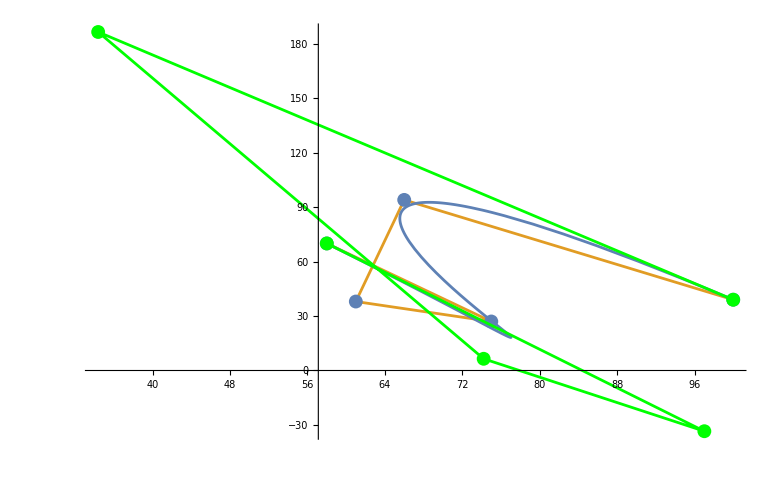

{False,13.4692}

```mathematica
cp
nn ={{1,1,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0},{1,1,0,0,0,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,0},{1,0,0,0,1,0,0,1,0,1,0,1,0,1,1,0,1,1,1,1,1,0},{0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1,0,0,0,1,0,1,1,0,0,1,1,0,0,0},{1,0,1,1,1,0,0,0,1,1,0,0,1,0,1,1,1,0,1,1,0,1},{1,1,0,1,1,1,0,1,1,0,0,0,0,1,0,1,0,0,0,1,0,1}};
nn = N[MatMul[cp, nn]];
nn = SetC1n[cp ,nn[[All, ;;-2]]]
newPlot = ParametricPlot[Bezier[nn, t], {t,0,1}];
nnPlot = ListPlot[{nn,nn}, Joined->{False, True}, PlotStyle->Green];
cpPlot =  ListPlot[{cp, cp}, Joined->{False, True}];
Show[cpPlot, newPlot,nnPlot, PlotRange->All]
TerminationCriteria[cp,nn, 1 ]
```

{{0.,0.},{1.25664,0.951057},{2.51327,0.587785},{3.76991,-0.587785},{5.02655,-0.951057},{6.28319,0.}}

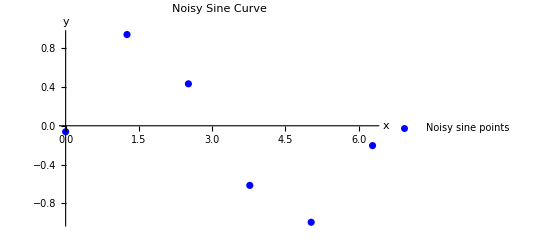

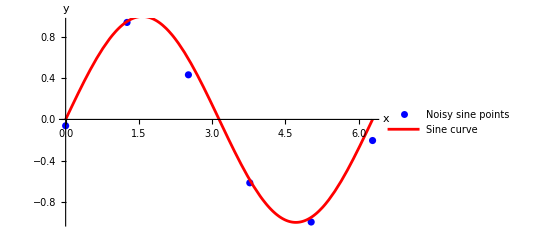

```mathematica
(*Generate x-values*)x=Range[0,2 Pi,(2 Pi)/5];

(*Generate sine values*)
y=Sin[x];
Print[N[Transpose[{x,y}]]]
(*Add noise*)
noise=RandomVariate[NormalDistribution[0,0.1],Length[y]];
yNoisy=y+noise;

(*Plot the points*)
ListPlot[Transpose[{x,yNoisy}],PlotStyle->Blue,PlotLegends->{"Noisy sine points"},PlotLabel->"Noisy Sine Curve",AxesLabel->{"x","y"}]

(*Plot the sine curve*)
Show[ListPlot[Transpose[{x,yNoisy}],PlotStyle->Blue,PlotLegends->{"Noisy sine points"},AxesLabel->{"x","y"}],Plot[Sin[x],{x,0,2 Pi},PlotStyle->Red,PlotLegends->{"Sine curve"}]]
```